# CS 478

## Scott Leland Crossen

## Perceptron Project

### Definitions

```mathematica
plotBinaryPerceptronLine[weight1_, weight2_,weightBias_] := Plot[y/.(Solve[weight1*x+weight2*y+weightBias==0,y][[1]]),{x,-1,1}, PlotRange->{-1,1} ,PlotLegends->{"Perceptron Weight Vector"}, PlotStyle ->{ Black,10}]
plotBinaryPerceptronData[data_]:=ListPlot[data,PlotRange->{{-1.1,1.1},{-1.1,1.1}}, AxesLabel->{Style["feature x", Black],Style["feature y", Black]}, PlotLabel->Style["Linear Data Perceptron", Black], PlotStyle->{Blue, Red},PlotMarkers-> {●,10}]
```

### Part 1

The code that implements the perceptron rule is included with the submission of this project. It is written in Scala and follows the functional paradigm.

### Part 2

Below are the true constructed ARFF files. the first is linearly separable and the second is not.

%This is linearly seperable
@RELATION custom1
@ATTRIBUTE fact1	Continuous
@ATTRIBUTE fact2 	Continuous
@ATTRIBUTE class 	{True,False}

@DATA
-0.6,-0.6,True
1.0,0.0,False
0.5,-0.75,False
-0.5,0.8,True
0.0,-1.0,True
1.0,0.5,False
0.75,1.0,True
0.75,-0.1,False | %This is not linearly seperable
@RELATION custom2
@ATTRIBUTE fact1	Continuous
@ATTRIBUTE fact2 	Continuous
@ATTRIBUTE class 	{True,False}

@DATA
-0.15,-0.2,False
0.05,0.8,True
0.65,0.2,True
-0.5,-0.75,True
-0.05,0.2,False
-0.25,0.05,False
-0.75,0.1,True
0.05,-0.1,False

### Part 3

For the purposes of this project, the stopping criteria is considered to be fulfilled when a continuous 5 epochs of the training set improved the weight vector by less than a cumulative 1.5 (half of the amount of features) across the feature vector times the learning constant. This value was chosen so that a smaller learning constant would be taken into account and allow the algorithm to arrive at a more precise result. Moreover, under this value a larger feature set allows more ability for the algorithm to change before stopping. This is why the overall equation is written this way.

The results show that the learning constant doesn’t really affect the amount of time it takes to train the perceptron. Data is given below showing the amount of epochs it takes to converge vs the learning constant. For a given single learning constant it was observed that a larger learning constant resulted in more sporadic changes in the weight vector whereas a smaller learning constant was more gradual in achieving the optimal solution. This of course is probably a result of the more-volatile nature of a larger training constant.

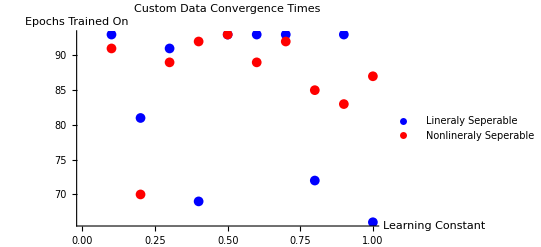

```mathematica
data={{.1,93,91},{.2,81,70},{.3,91,89},{.4,69,92},{.5,93,93},{.6,93,89},{.7,93,92},{.8,72,85},{.9,93,83},{1,66,87}};
ListPlot[{Transpose[{Transpose[data][[1]],Transpose[data][[2]]}],Transpose[{Transpose[data][[1]],Transpose[data][[3]]}]}, AxesLabel->{Style["Learning Constant", Black],Style["Epochs Trained On", Black]}, PlotLabel->Style["Custom Data Convergence Times", Black], PlotStyle->{Blue, Red},PlotMarkers-> {●,10}, PlotLegends->{"Lineraly Seperable", "Nonlineraly Seperable"}]
```

### Part 4

The below plots show the two different solutions to the above ARFF files. The first shows a correct separation of the data and the second shows a poor separation of the data (because it is not linearly separable)

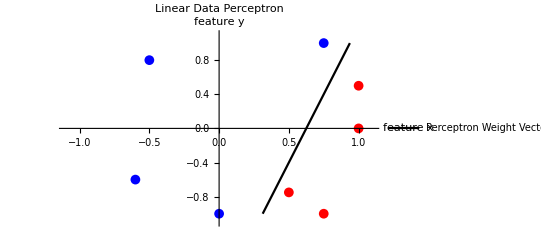

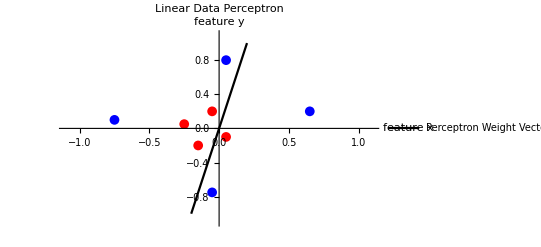

```mathematica
Show[
plotBinaryPerceptronData[{{{-.6,-.6},{-.5,.8},{0,-1},{.75,1}},{{1,0},{.5,-.75},{1,.5},{.75,-1}}}],
plotBinaryPerceptronLine[-0.16,0.05000000000000001,0.1]
]
Show[
plotBinaryPerceptronData[{{{.05,.8},{.65,.2},{-.05,-.75},{-.75,.1}},{{-.05,.2},{-.25,.05},{-.15, -.2},{.05,-.1}}}],
plotBinaryPerceptronLine[-0.05000000000000002,0.009999999999999995,0.0]
]
```

### Part 5

For a perceptron that is forced to train on all the data we found an accuracy in the 90s. The plots below show the results for 5 trials.

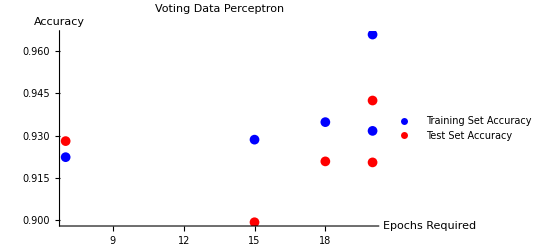

The average amount of epochs trained on was 16.

The average training accuracy was 0.936646

The average testing accuracy was 0.92223

```mathematica
accuracy = {{15,0.9285714285714286,0.8992805755395683},{20,0.9316770186335404,0.9205035971223022},{7,0.922360248447205,0.9280575539568345},{18,0.9347826086956522,0.920863309352518},{20,0.9658385093167702,0.9424460431654677}};
ListPlot[{Transpose[{accuracy[[All,1]],accuracy[[All, 2]]}],Transpose[{accuracy[[All,1]],accuracy[[All, 3]]}]}, AxesLabel->{Style["Epochs Required", Black],Style["Accuracy", Black]}, PlotLabel->Style["Voting Data Perceptron", Black], PlotStyle->{Blue, Red},PlotMarkers-> {●,10}, PlotLegends->{"Training Set Accuracy", "Test Set Accuracy"}]
Print["The average amount of epochs trained on was ", N[Mean[accuracy[[All,1]]]]]
Print["The average training accuracy was ", N[Mean[accuracy[[All,2]]]]]
Print["The average testing accuracy was ", N[Mean[accuracy[[All,3]]]]]
```

For this  data set a good stopping criteria was determined to be when the perceptron reached 5 successive iterations of it’s data set with no significant increase in the weight vector. A significant increase is considered to be when the summed changed in the weight vector is more than 1/2 times the number of features times the training constant. The logic behind this algorithm is explained more fully in part 3 of this project.

The final weight vector for a perceptron with a test accuracy of 96 % turns out to be {0.0, 0.47336482815648373, 1.1834120703912094, -1.6567768985476934, 0.0, 0.23668241407824187, -0.23668241407824187, -0.23668241407824187, 0.9467296563129675, -0.47336482815648373, 0.7100472422347256, -0.47336482815648373, 0.47336482815648373, -0.23668241407824187, 0.9467296563129675, -0.23668241407824187, 0.47336482815648373}.
According to this data, there is a slight offset (bias) in the data. Moreover, the 3rd and 4th features seem to be the most influential with the 1st and 5th features being least influential. It’s important to note that not all returned weight vectors had a bias. The most-accurate ones all did though. Note that the longer the perceptron was allowed to train the more accurate it tended to be. This is best shown by the upward-sloping trend in the above plot.

Most influential features: 3, 4
Least Influential features: 1, 5

Below is a plot of average misclassification rate vs epochs elapsed. It would appear that not much improvement happens after the first epoch. Though the graph below would have stopped much earlier than 50 epochs, I suspended the halting criteria to demonstrate the misclassification rate over a longer period. Again, I suspect that the misclassification rate would not be so noisy if I allowed for a smaller time frame. More than that, but it is likely that my perceptron was able to accurately train itself after one epoch and continuing the training was just overkill.

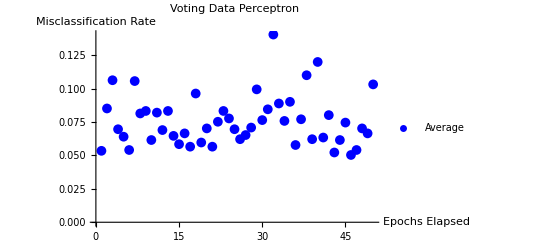

```mathematica
data1 =Transpose[{Range[100],{0.06521739130434778,0.04347826086956519,0.10248447204968947,0.0496894409937888,0.04658385093167705,0.0496894409937888,0.03416149068322982,0.06521739130434778,0.10248447204968947,0.03416149068322982,0.04037267080745344,0.06211180124223603,0.09316770186335399,0.05900621118012417,0.03105590062111796,0.06521739130434778,0.03105590062111796,0.04658385093167705,0.05590062111801242,0.04347826086956519,0.03416149068322982,0.04347826086956519,0.0714285714285714,0.03416149068322982,0.07763975155279501,0.08074534161490687,0.03105590062111796,0.04658385093167705,0.04347826086956519,0.037267080745341574,0.05590062111801242,0.23291925465838514,0.04037267080745344,0.09316770186335399,0.04037267080745344,0.05590062111801242,0.05590062111801242,0.15527950310559002,0.08695652173913049,0.33229813664596275,0.037267080745341574,0.04658385093167705,0.04347826086956519,0.04658385093167705,0.03416149068322982,0.037267080745341574,0.0496894409937888,0.04347826086956519,0.03105590062111796,0.06211180124223603,0.08074534161490687,0.06211180124223603,0.04658385093167705,0.05590062111801242,0.09627329192546585,0.05900621118012417,0.06211180124223603,0.04037267080745344,0.05900621118012417,0.04347826086956519,0.04037267080745344,0.04347826086956519,0.07453416149068326,0.052795031055900665,0.04037267080745344,0.06521739130434778,0.09627329192546585,0.037267080745341574,0.052795031055900665,0.052795031055900665,0.28881987577639756,0.04347826086956519,0.08074534161490687,0.04347826086956519,0.07763975155279501,0.20186335403726707,0.09627329192546585,0.05590062111801242,0.052795031055900665,0.037267080745341574,0.04037267080745344,0.03416149068322982,0.13043478260869568,0.08074534161490687,0.052795031055900665,0.037267080745341574,0.052795031055900665,0.18322981366459623,0.03105590062111796,0.13354037267080743,0.07763975155279501,0.052795031055900665,0.1273291925465838,0.04037267080745344,0.03416149068322982,0.037267080745341574,0.05590062111801242,0.10869565217391308,0.06211180124223603,0.04037267080745344}}];
data2 =Transpose[{Range[100],{0.05900621118012417,0.1708074534161491,0.06211180124223603,0.04347826086956519,0.08695652173913049,0.052795031055900665,0.0714285714285714,0.1149068322981367,0.06832298136645965,0.06832298136645965,0.1645962732919255,0.05900621118012417,0.08695652173913049,0.04658385093167705,0.06521739130434778,0.0496894409937888,0.0496894409937888,0.10248447204968947,0.0496894409937888,0.09006211180124224,0.052795031055900665,0.052795031055900665,0.06832298136645965,0.09006211180124224,0.0496894409937888,0.0496894409937888,0.0496894409937888,0.052795031055900665,0.17391304347826086,0.07763975155279501,0.18012422360248448,0.10869565217391308,0.11180124223602483,0.04037267080745344,0.08385093167701863,0.04347826086956519,0.0993788819875776,0.05590062111801242,0.04347826086956519,0.06211180124223603,0.05590062111801242,0.052795031055900665,0.05900621118012417,0.052795031055900665,0.06521739130434778,0.04658385093167705,0.04658385093167705,0.05590062111801242,0.04037267080745344,0.1428571428571429,0.052795031055900665,0.052795031055900665,0.06521739130434778,0.0993788819875776,0.052795031055900665,0.08695652173913049,0.052795031055900665,0.052795031055900665,0.0496894409937888,0.11180124223602483,0.13975155279503104,0.0714285714285714,0.052795031055900665,0.037267080745341574,0.05590062111801242,0.06521739130434778,0.052795031055900665,0.037267080745341574,0.08385093167701863,0.2857142857142857,0.052795031055900665,0.0496894409937888,0.05590062111801242,0.09316770186335399,0.14596273291925466,0.1925465838509317,0.06521739130434778,0.05900621118012417,0.0496894409937888,0.19875776397515532,0.05900621118012417,0.04347826086956519,0.09627329192546585,0.04037267080745344,0.10559006211180122,0.04658385093167705,0.052795031055900665,0.06211180124223603,0.0714285714285714,0.052795031055900665,0.1273291925465838,0.09316770186335399,0.06211180124223603,0.05590062111801242,0.06521739130434778,0.3012422360248447,0.052795031055900665,0.04037267080745344,0.052795031055900665,0.04658385093167705}}];
data3 =Transpose[{Range[100],{0.04658385093167705,0.06211180124223603,0.06211180124223603,0.11180124223602483,0.09316770186335399,0.06211180124223603,0.05590062111801242,0.05900621118012417,0.0496894409937888,0.09316770186335399,0.0714285714285714,0.07763975155279501,0.06211180124223603,0.05900621118012417,0.0714285714285714,0.0714285714285714,0.08385093167701863,0.0993788819875776,0.05900621118012417,0.0496894409937888,0.03416149068322982,0.05900621118012417,0.13354037267080743,0.13975155279503104,0.0496894409937888,0.04347826086956519,0.0496894409937888,0.13975155279503104,0.04658385093167705,0.08385093167701863,0.052795031055900665,0.1211180124223602,0.10559006211180122,0.10248447204968947,0.05900621118012417,0.05590062111801242,0.08695652173913049,0.0496894409937888,0.05900621118012417,0.04037267080745344,0.06211180124223603,0.1708074534161491,0.04347826086956519,0.03416149068322982,0.06832298136645965,0.07453416149068326,0.03105590062111796,0.13354037267080743,0.07763975155279501,0.1211180124223602,0.08695652173913049,0.18322981366459623,0.037267080745341574,0.04658385093167705,0.08385093167701863,0.11180124223602483,0.07453416149068326,0.07453416149068326,0.1273291925465838,0.08074534161490687,0.04658385093167705,0.09627329192546585,0.06832298136645965,0.04658385093167705,0.06211180124223603,0.06832298136645965,0.0993788819875776,0.0496894409937888,0.05900621118012417,0.04347826086956519,0.0714285714285714,0.04347826086956519,0.09627329192546585,0.05590062111801242,0.10559006211180122,0.06832298136645965,0.06211180124223603,0.04658385093167705,0.06521739130434778,0.06832298136645965,0.10869565217391308,0.06521739130434778,0.04658385093167705,0.07763975155279501,0.05590062111801242,0.21118012422360244,0.05900621118012417,0.06521739130434778,0.1863354037267081,0.06211180124223603,0.05900621118012417,0.10559006211180122,0.1273291925465838,0.052795031055900665,0.3571428571428571,0.10248447204968947,0.0496894409937888,0.1149068322981367,0.05900621118012417,0.04347826086956519}}];
data4 =Transpose[{Range[100],{0.03416149068322982,0.05900621118012417,0.24844720496894412,0.052795031055900665,0.052795031055900665,0.0496894409937888,0.10869565217391308,0.09316770186335399,0.1428571428571429,0.04037267080745344,0.06832298136645965,0.07453416149068326,0.1149068322981367,0.06832298136645965,0.05900621118012417,0.08385093167701863,0.05900621118012417,0.05590062111801242,0.05590062111801242,0.08385093167701863,0.10869565217391308,0.13043478260869568,0.06211180124223603,0.06211180124223603,0.1211180124223602,0.06832298136645965,0.07453416149068326,0.06211180124223603,0.17391304347826086,0.05900621118012417,0.0496894409937888,0.17701863354037262,0.0993788819875776,0.0496894409937888,0.1490683229813664,0.0714285714285714,0.08695652173913049,0.2080745341614907,0.052795031055900665,0.03105590062111796,0.06832298136645965,0.0714285714285714,0.052795031055900665,0.06211180124223603,0.04037267080745344,0.037267080745341574,0.07453416149068326,0.052795031055900665,0.1149068322981367,0.11801242236024845,0.10869565217391308,0.05590062111801242,0.03416149068322982,0.07453416149068326,0.06211180124223603,0.26086956521739135,0.05590062111801242,0.0496894409937888,0.03105590062111796,0.052795031055900665,0.1645962732919255,0.05900621118012417,0.037267080745341574,0.052795031055900665,0.05590062111801242,0.1149068322981367,0.06832298136645965,0.08074534161490687,0.0993788819875776,0.20496894409937894,0.07763975155279501,0.0496894409937888,0.05590062111801242,0.08385093167701863,0.05590062111801242,0.05900621118012417,0.0496894409937888,0.05590062111801242,0.037267080745341574,0.04037267080745344,0.07453416149068326,0.05900621118012417,0.05900621118012417,0.04037267080745344,0.04037267080745344,0.04347826086956519,0.07453416149068326,0.06521739130434778,0.05590062111801242,0.037267080745341574,0.10248447204968947,0.06521739130434778,0.04037267080745344,0.04347826086956519,0.0496894409937888,0.052795031055900665,0.03416149068322982,0.04037267080745344,0.09316770186335399,0.11180124223602483}}];
data5 =Transpose[{Range[100],{0.06211180124223603,0.09006211180124224,0.05590062111801242,0.09006211180124224,0.04037267080745344,0.05590062111801242,0.2577639751552795,0.07453416149068326,0.052795031055900665,0.0714285714285714,0.06521739130434778,0.0714285714285714,0.05900621118012417,0.09006211180124224,0.06521739130434778,0.06211180124223603,0.05900621118012417,0.17701863354037262,0.07763975155279501,0.08385093167701863,0.052795031055900665,0.09006211180124224,0.08074534161490687,0.06211180124223603,0.0496894409937888,0.06832298136645965,0.1211180124223602,0.052795031055900665,0.05900621118012417,0.12422360248447206,0.08385093167701863,0.06211180124223603,0.08695652173913049,0.09316770186335399,0.11801242236024845,0.06211180124223603,0.05590062111801242,0.08074534161490687,0.06832298136645965,0.13354037267080743,0.09316770186335399,0.05900621118012417,0.06211180124223603,0.11180124223602483,0.1645962732919255,0.05590062111801242,0.06832298136645965,0.06521739130434778,0.06832298136645965,0.0714285714285714,0.07763975155279501,0.15527950310559002,0.12422360248447206,0.05900621118012417,0.05900621118012417,0.052795031055900665,0.17391304347826086,0.09627329192546585,0.10869565217391308,0.08074534161490687,0.28260869565217395,0.05900621118012417,0.0496894409937888,0.06211180124223603,0.08385093167701863,0.04347826086956519,0.06521739130434778,0.052795031055900665,0.05590062111801242,0.16149068322981364,0.10869565217391308,0.08695652173913049,0.07453416149068326,0.05590062111801242,0.07453416149068326,0.23913043478260865,0.06521739130434778,0.05590062111801242,0.06521739130434778,0.06211180124223603,0.07453416149068326,0.08695652173913049,0.07763975155279501,0.06521739130434778,0.06211180124223603,0.05590062111801242,0.07763975155279501,0.06211180124223603,0.08385093167701863,0.0714285714285714,0.08074534161490687,0.05900621118012417,0.06832298136645965,0.08385093167701863,0.07453416149068326,0.0496894409937888,0.052795031055900665,0.05590062111801242,0.21739130434782605,0.06832298136645965}}];
data = (data1+data2+data3+data4+data5)/5;
ListPlot[data[[1;;50,All]], AxesLabel->{Style["Epochs Elapsed", Black],Style["Misclassification Rate", Black]}, PlotLabel->Style["Voting Data Perceptron", Black], PlotStyle->Blue,PlotMarkers-> {●,10}, PlotLegends->{"Average"}]
```

### Part 6

For this part I created two different perceptrons to solve the iris data set. The two perceptrons are the same as described in the problem statement. The perceptron described in part (a) is called a individual-test perceptron. The perceptron described in part (b) is called the matched-pairs perceptron. Each implementation can be found in the code included in the submission of this project.

Each perceptron was allowed to train on 70% of the data and then test the remaining 30%. Only one epoch was used in order to demonstrate baseline viability. Stopping criteria was found not to affect the overall results and so was not included for consistency.

As shown by the data, the matched pairs perceptron achieved a higher and more stable accuracy compared to the individual perceptron model. In fact, it would appear as if in almost every case the matched pairs model performed better than the individual selection model. Average accuracy is included for reference. I propose that the results are because the matched pairs experiment is a more defined experiment - The machine only needs to separate between two sets of data rather than 3 at a time. For example, it is conceivable to have three sets of data with one set in the middle. A individually-selecting perceptron would not be able to separate this middle portion from the two outside portions whereas the matched-pairs perceptron could. This is why the matched-pairs perceptron is likely better.

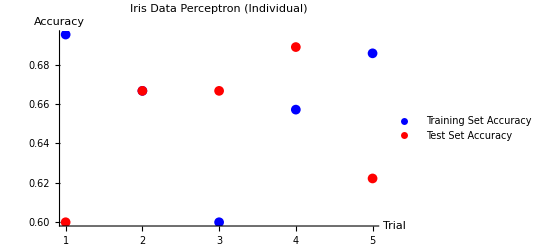

The average training accuracy was 0.660952

The average testing accuracy was 0.648889

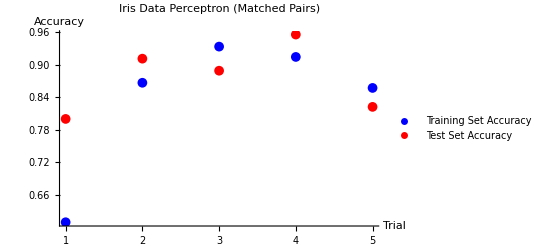

The average training accuracy was 0.83619

The average testing accuracy was 0.875556

```mathematica
IndividualAccuracy = {{1,0.6952380952380952,0.6},{2,0.6666666666666666,0.6666666666666666},{3,0.6,0.6666666666666666},{4,0.6571428571428571,0.6888888888888889},{5,0.6857142857142857,0.6222222222222222}};
matchedPairsAccuracy = {{1,0.6095238095238096,0.8},{2,0.8666666666666667,0.9111111111111111},{3,0.9333333333333333,0.8888888888888888},{4,0.9142857142857143,0.9555555555555556},{5,0.8571428571428571,0.8222222222222222}};
ListPlot[{Transpose[{IndividualAccuracy[[All,1]],IndividualAccuracy[[All, 2]]}],Transpose[{IndividualAccuracy[[All,1]],IndividualAccuracy[[All, 3]]}]}, AxesLabel->{Style["Trial", Black],Style["Accuracy", Black]}, PlotLabel->Style["Iris Data Perceptron (Individual)", Black], PlotStyle->{Blue, Red},PlotMarkers-> {●,10}, PlotLegends->{"Training Set Accuracy", "Test Set Accuracy"}]
Print["The average training accuracy was ", N[Mean[IndividualAccuracy[[All,2]]]]]
Print["The average testing accuracy was ", N[Mean[IndividualAccuracy[[All,3]]]]]
ListPlot[{Transpose[{matchedPairsAccuracy[[All,1]],matchedPairsAccuracy[[All, 2]]}],Transpose[{matchedPairsAccuracy[[All,1]],matchedPairsAccuracy[[All, 3]]}]}, AxesLabel->{Style["Trial", Black],Style["Accuracy", Black]}, PlotLabel->Style["Iris Data Perceptron (Matched Pairs)", Black], PlotStyle->{Blue, Red},PlotMarkers-> {●,10}, PlotLegends->{"Training Set Accuracy", "Test Set Accuracy"}]
Print["The average training accuracy was ", N[Mean[matchedPairsAccuracy[[All,2]]]]]
Print["The average testing accuracy was ", N[Mean[matchedPairsAccuracy[[All,3]]]]]
```